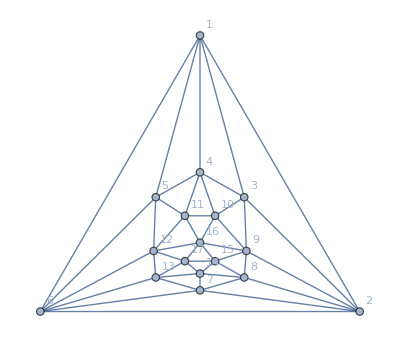

```mathematica
Graph[plantri[[10]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
EmbedGraph5Bis[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,3,4,5,6}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10]]],1];
g=EdgeDelete[ g,{2<->3,3<->4,4<->5,5<->6,6<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
plantri[[1]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}

```mathematica
dddd=Monitor[Table[allGraphs[k,"colofour"]->EmbedGraph5Bis[allGraphs,k],{k,atomKeys}],k];Length[dddd]
```

52

```mathematica
demoValues=Monitor[Table[d[[1]]->ChromaticPolynomial[d[[2]],4]/24,{d,dddd}],d]
```

{v1x2x3x4x5→0,v1x2x3x45→10,v1x2x35x4→4,v1x2x34x5→12,v1x2x345→18,v1x25x3x4→10,v1x25x34→16,v1x24x3x5→12,v1x24x35→8,v1x245x3→14,v1x23x4x5→12,v1x23x45→16,v1x235x4→12,v1x234x5→28,v1x2345→20,v15x2x3x4→6,v15x2x34→14,v15x24x3→12,v15x23x4→14,v15x234→20,v14x2x3x5→10,v14x2x35→6,v14x25x3→12,v14x23x5→16,v14x235→8,v145x2x3→20,v145x23→22,v13x2x4x5→4,v13x2x45→8,v13x25x4→6,v13x24x5→8,v13x245→6,v135x2x4→10,v135x24→8,v134x2x5→12,v134x25→8,v1345x2→18,v12x3x4x5→10,v12x3x45→16,v12x35x4→8,v12x34x5→16,v12x345→14,v125x3x4→20,v125x34→22,v124x3x5→14,v124x35→6,v1245x3→18,v123x4x5→18,v123x45→14,v1235x4→18,v1234x5→20,v12345→18}

```mathematica
Sort[demoValues,#1[[2]]<#2[[2]]&]/.repcolofourgraph
```

{-Graphics-v1x2x3x4x529524→0,-Graphics-v13x2x4x536085→4,-Graphics-v1x2x35x429527→4,-Graphics-v124x3551478→6,-Graphics-v13x24536194→6,-Graphics-v13x25x436112→6,-Graphics-v14x2x3531714→6,-Graphics-v15x2x3x430253→6,-Graphics-v12x35x449210→8,-Graphics-v134x2538308→8,-Graphics-v135x2436898→8,-Graphics-v13x24x536166→8,-Graphics-v13x2x4536086→8,-Graphics-v14x23531984→8,-Graphics-v1x24x3529608→8,-Graphics-v12x3x4x549207→10,-Graphics-v135x2x436817→10,-Graphics-v14x2x3x531711→10,-Graphics-v1x25x3x429551→10,-Graphics-v1x2x3x4529525→10,-Graphics-v134x2x538281→12,-Graphics-v14x25x331738→12,-Graphics-v15x24x330334→12,-Graphics-v1x235x429797→12,-Graphics-v1x23x4x529767→12,-Graphics-v1x24x3x529605→12,-Graphics-v1x2x34x529533→12,-Graphics-v123x4556012→14,-Graphics-v124x3x551475→14,-Graphics-v12x34549220→14,-Graphics-v15x23x430496→14,-Graphics-v15x2x3430262→14,-Graphics-v1x245x329633→14,-Graphics-v12x34x549216→16,-Graphics-v12x3x4549208→16,-Graphics-v14x23x531954→16,-Graphics-v1x23x4529768→16,-Graphics-v1x25x3429560→16,-Graphics-v1234559048→18,-Graphics-v1235x456770→18,-Graphics-v123x4x556011→18,-Graphics-v1245x352232→18,-Graphics-v1345x239014→18,-Graphics-v1x2x34529537→18,-Graphics-v1234x558288→20,-Graphics-v125x3x449963→20,-Graphics-v145x2x332441→20,-Graphics-v15x23430586→20,-Graphics-v1x234529888→20,-Graphics-v125x3449972→22,-Graphics-v145x2332684→22,-Graphics-v1x234x529857→28}

```mathematica
..
```

```mathematica
ExpressionsToGraphBis[list_]:=Block[{result={},left,newNode=-1,currentBis,vertexLabels, vertices={},key,mat2,vertexStyle={},vertexLabels2={},vertexStyle2={},sumKey,crit},
Table[
If[Length[current]==0,
result=Append[result,current->newNode ],

currentBis=Select[current,ToString[#]≠"v1x2x3x4x5"&];
crit = Fold[Plus,current];
sumKey=First[Select[Keys[allGraphs],(allGraphs[#,"colofour"]==crit)/.repZero&]];
newNode=sumKey;
vertexLabels2=Append[vertexLabels2,sumKey->Labeled[allGraphs[sumKey,"graph"],allGraphs[sumKey,"colofour"]/.demoValues]];
vertexStyle2=Append[vertexStyle2,sumKey->ColourForKey[allGraphs,sumKey]];
Table[
result=Append[result,currentBis[[k]]->newNode];
vertices=Append[vertices,currentBis[[k]]]
,{k,Length[currentBis]}
];
];

(*result=Append[result,newNode->0];*)
newNode=newNode-1
,
{current,list}
];
vertices = DeleteDuplicates[vertices];
vertexLabels=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;
mat2=allGraphs[key,"matrix"];
v->Tooltip[
Labeled[
allGraphs[key]["graph"],{v,v/.demoValues}],
Labeled[
Column[
{
Style[key,Bold],
MatrixForm[mat2,TableHeadings->{Table[Style[k,Red],{k,TheSize}],Table[Style[k,Red],{k,TheSize}]}]
,
Row[{
allGraphs[key]["graph"],
Graph[
VertexList[allGraphs[key]["graph"]],
EdgeList[allGraphs[key]["graph"]],
VertexLabels->PropertyValue[allGraphs[key]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[allGraphs[key]["parents"],Italic],
Style[allGraphs[key]["colofour"],Italic]
},
Center
],Style[allGraphs[key]["compwhy"],Bold]]]

,{v,vertices}];
vertexStyle=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;v->ColourForKey[allGraphs,key],{v,vertices}];
Graph[result,VertexLabels->Join[vertexLabels,vertexLabels2],VertexStyle->Join[vertexStyle,vertexStyle2]]
]
```

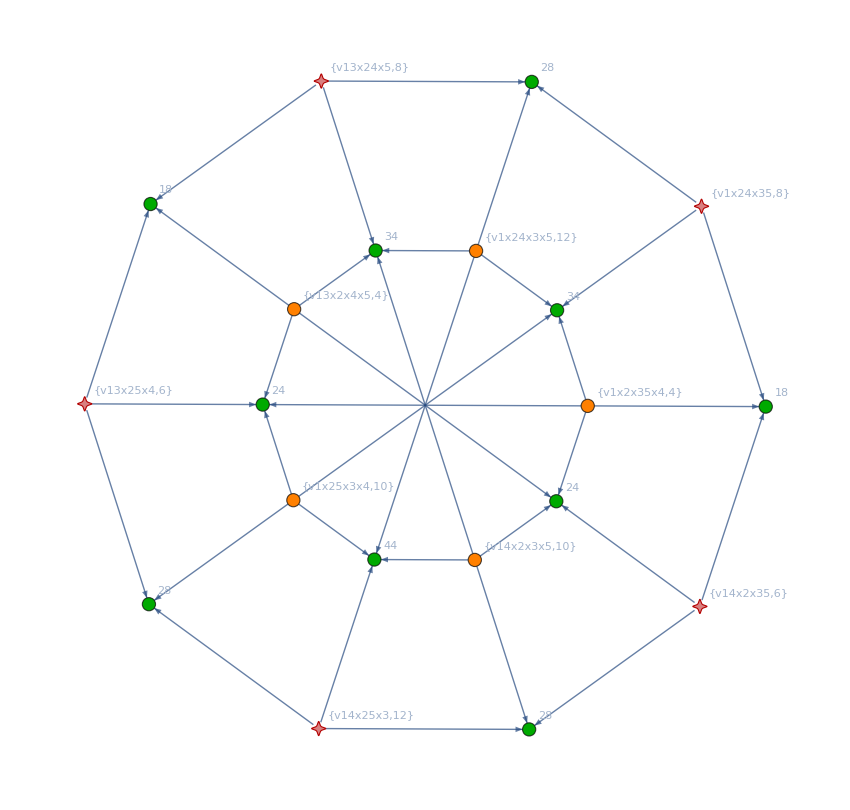

```mathematica
Graph[ExpressionsToGraphBis[Select[PositiveExpressions,Length[#]>2&]],GraphLayout->"HighDimensionalEmbedding", GraphHighlight->important, GraphHighlightStyle->"VertexConcaveDiamond",ImageSize->850]
```